```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.0001,1,0]],B:=Inverse[β[ω,0.0001,1,0]],T1:=T1[1]},Do[J=Inverse[IdentityMatrix[14]-B.ConjugateTranspose[T1].J.T1].B,8000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

```mathematica
tr[1,0.0001,1,0]
```

2.99292

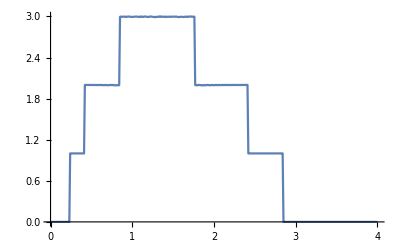

```mathematica
ListLinePlot[Table[{ω,tr[ω,0.0001,1,0]},{ω,0,4,0.01}]]
```

```mathematica
k31:=k31=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp3.dat"]][ω]},{ω,0,2,0.001}]
k32:=k32=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/2imp/2imp3.dat"]][ω]},{ω,0,2,0.001}]
k33:=k33=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/3imp/3imp3.dat"]][ω]},{ω,0,2,0.001}]
k34:=k34=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/4imp/4imp3.dat"]][ω]},{ω,0,2,0.001}]
k35:=k35=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/5imp/5imp3.dat"]][ω]},{ω,0,2,0.001}]
k36:=k36=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/6imp/6imp3.dat"]][ω]},{ω,0,2,0.001}]
k37:=k37=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/7imp/7imp3.dat"]][ω]},{ω,0,2,0.001}]
```

```mathematica
f3[ω_]:={{0,Pri[ω]},{1,k31[[ω*1000+1]][[2]]},{2,k32[[ω*1000+1]][[2]]},{3,k33[[ω*1000+1]][[2]]},{4,k34[[ω*1000+1]][[2]]},{5,k35[[ω*1000+1]][[2]]},{6,k36[[ω*1000+1]][[2]]},{7,k37[[ω*1000+1]][[2]]}}
```

```mathematica
k41:=k41=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp4.dat"]][ω]},{ω,0,2,0.001}]
k42:=k42=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/2imp/2imp4.dat"]][ω]},{ω,0,2,0.001}]
k43:=k43=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/3imp/3imp4.dat"]][ω]},{ω,0,2,0.001}]
k44:=k44=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/4imp/4imp4.dat"]][ω]},{ω,0,2,0.001}]
k45:=k45=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/5imp/5imp4.dat"]][ω]},{ω,0,2,0.001}]
k46:=k46=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/6imp/6imp4.dat"]][ω]},{ω,0,2,0.001}]
k47:=k47=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/7imp/7imp4.dat"]][ω]},{ω,0,2,0.001}]
```

```mathematica
f4[ω_]:={{0,Pri[ω]},{1,k41[[ω*1000+1]][[2]]},{2,k42[[ω*1000+1]][[2]]},{3,k43[[ω*1000+1]][[2]]},{4,k44[[ω*1000+1]][[2]]},{5,k45[[ω*1000+1]][[2]]},{6,k46[[ω*1000+1]][[2]]},{7,k47[[ω*1000+1]][[2]]}}
```

```mathematica
k51:=k51=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp5.csv"]][ω]},{ω,0,2,0.001}]
k52:=k52=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/2imp/2imp5.csv"]][ω]},{ω,0,2,0.001}]
k53:=k53=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/3imp/3imp5.csv"]][ω]},{ω,0,2,0.001}]
k54:=k54=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/4imp/4imp5.csv"]][ω]},{ω,0,2,0.001}]
k55:=k55=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/5imp/5imp5.csv"]][ω]},{ω,0,2,0.001}]
k56:=k56=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/6imp/6imp5.csv"]][ω]},{ω,0,2,0.001}]
k57:=k57=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/7imp/7imp5.csv"]][ω]},{ω,0,2,0.001}]
```

```mathematica
f5[ω_]:={{0,Pri[ω]},{1,k51[[ω*1000+1]][[2]]},{2,k52[[ω*1000+1]][[2]]},{3,k53[[ω*1000+1]][[2]]},{4,k54[[ω*1000+1]][[2]]},{5,k55[[ω*1000+1]][[2]]},{6,k56[[ω*1000+1]][[2]]},{7,k57[[ω*1000+1]][[2]]}}
```

```mathematica
k61:=k61=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp6.dat"]][ω]},{ω,0,2,0.001}]
k62:=k62=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/2imp/2imp6.dat"]][ω]},{ω,0,2,0.001}]
k63:=k63=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/3imp/3imp6.dat"]][ω]},{ω,0,2,0.001}]
k64:=k64=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/4imp/4imp6.dat"]][ω]},{ω,0,2,0.001}]
k65:=k65=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/5imp/5imp6.dat"]][ω]},{ω,0,2,0.001}]
k66:=k66=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/6imp/6imp6.dat"]][ω]},{ω,0,2,0.001}]
k67:=k67=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/7imp/7imp6.dat"]][ω]},{ω,0,2,0.001}]
```

```mathematica
f6[ω_]:={{0,Pri[ω]},{1,k61[[ω*1000+1]][[2]]},{2,k62[[ω*1000+1]][[2]]},{3,k63[[ω*1000+1]][[2]]},{4,k64[[ω*1000+1]][[2]]},{5,k65[[ω*1000+1]][[2]]},{6,k66[[ω*1000+1]][[2]]},{7,k67[[ω*1000+1]][[2]]}}
```

```mathematica
k71:=k71=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp7.dat"]][ω]},{ω,0,2,0.001}]
k72:=k72=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/2imp/2imp7.dat"]][ω]},{ω,0,2,0.001}]
k73:=k73=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/3imp/3imp7.dat"]][ω]},{ω,0,2,0.001}]
k74:=k74=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/4imp/4imp7.dat"]][ω]},{ω,0,2,0.001}]
k75:=k75=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/5imp/5imp7.dat"]][ω]},{ω,0,2,0.001}]
k76:=k76=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/6imp/6imp7.dat"]][ω]},{ω,0,2,0.001}]
k77:=k77=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/7imp/7imp7.dat"]][ω]},{ω,0,2,0.001}]
```

```mathematica
f7[ω_]:={{0,Pri[ω]},{1,k71[[ω*1000+1]][[2]]},{2,k72[[ω*1000+1]][[2]]},{3,k73[[ω*1000+1]][[2]]},{4,k74[[ω*1000+1]][[2]]},{5,k75[[ω*1000+1]][[2]]},{6,k76[[ω*1000+1]][[2]]},{7,k77[[ω*1000+1]][[2]]}}
```

```mathematica
k81:=k81=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp8.dat"]][ω]},{ω,0,2,0.001}]
k82:=k82=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/2imp/2imp8.dat"]][ω]},{ω,0,2,0.001}]
k83:=k83=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/3imp/3imp8.dat"]][ω]},{ω,0,2,0.001}]
k84:=k84=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/4imp/4imp8.dat"]][ω]},{ω,0,2,0.001}]
k85:=k85=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/5imp/5imp8.dat"]][ω]},{ω,0,2,0.001}]
k86:=k86=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/6imp/6imp8.dat"]][ω]},{ω,0,2,0.001}]
k87:=k87=Table[{ω,Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/7imp/7imp8.dat"]][ω]},{ω,0,2,0.001}]
```

```mathematica
f8[ω_]:={{0,Pri[ω]},{1,k81[[ω*1000+1]][[2]]},{2,k82[[ω*1000+1]][[2]]},{3,k83[[ω*1000+1]][[2]]},{4,k84[[ω*1000+1]][[2]]},{5,k85[[ω*1000+1]][[2]]},{6,k86[[ω*1000+1]][[2]]},{7,k87[[ω*1000+1]][[2]]}}
```

```mathematica
f3[1]
```

{{0,Pri[1]},{1,2.74296},{2,2.54863},{3,2.36491},{4,2.20154},{5,2.07652},{6,1.96547},{7,2.04573}}

```mathematica
f4[1]
```

{{0,Pri[1]},{1,2.58652},{2,2.2583},{3,2.00625},{4,1.82239},{5,1.66895},{6,1.52405},{7,1.6117}}

```mathematica
f5[1]
```

{{0,Pri[1]},{1,2.39557},{2,1.96898},{3,1.63131},{4,1.39113},{5,1.20677},{6,1.04862},{7,0.917215}}

```mathematica
f6[1]
```

{{0,Pri[1]},{1,2.18938},{2,1.69109},{3,1.36637},{4,1.14862},{5,0.980308},{6,0.860522},{7,0.932534}}

```mathematica
f7[1]
```

{{0,Pri[1]},{1,2.00613},{2,1.44488},{3,1.11841},{4,0.89816},{5,0.768608},{6,0.672441},{7,0.724692}}

```mathematica
f8[1]
```

{{0,Pri[1]},{1,1.80024},{2,1.20914},{3,0.91212},{4,0.724},{5,0.633336},{6,0.553533},{7,0.580751}}

```mathematica
φ3[ω_]:=Interpolation[f3[ω]]
```

```mathematica
sloap3[ω_,n_]:=(φ3[ω][n]-φ3[ω][n+.1])/0.1
```

```mathematica
s3[ω_,l_]:=s3[ω,l]=Mean[Table[sloap3[ω,k],{k,Range[0,l,0.1]}]]
```

```mathematica
φ4[ω_]:=Interpolation[f4[ω]]
sloap4[ω_,n_]:=(φ4[ω][n]-φ4[ω][n+.1])/0.1
s4[ω_,l_]:=s4[ω,l]=Mean[Table[sloap4[ω,k],{k,Range[0,l,0.1]}]]
```

```mathematica
φ5[ω_]:=Interpolation[f5[ω]]
sloap5[ω_,n_]:=(φ5[ω][n]-φ5[ω][n+.1])/0.1
s5[ω_,l_]:=s5[ω,l]=Mean[Table[sloap5[ω,k],{k,Range[0,l,0.1]}]]
```

```mathematica
φ6[ω_]:=Interpolation[f6[ω]]
sloap6[ω_,n_]:=(φ6[ω][n]-φ6[ω][n+.1])/0.1
s6[ω_,l_]:=s6[ω,l]=Mean[Table[sloap6[ω,k],{k,Range[0,l,0.1]}]]
```

```mathematica
φ7[ω_]:=Interpolation[f7[ω]]
sloap7[ω_,n_]:=(φ7[ω][n]-φ7[ω][n+.1])/0.1
s7[ω_,l_]:=s7[ω,l]=Mean[Table[sloap7[ω,k],{k,Range[0,l,0.1]}]]
```

```mathematica
φ8[ω_]:=Interpolation[f8[ω]]
sloap8[ω_,n_]:=(φ8[ω][n]-φ8[ω][n+.1])/0.1
s8[ω_,l_]:=s8[ω,l]=Mean[Table[sloap8[ω,k],{k,Range[0,l,0.1]}]]
```

```mathematica
m5[ϵ1_,k_]:=Module[{Tin=T1[1],T=TT[1],(*μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}],*) μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={{imp8,imp,imp7,imp3,imp3,imp,imp,imp,imp,imp1,imp,imp,imp,imp,imp5,imp1,imp11,imp,imp13,imp,imp4,imp5,imp10,imp6,imp,imp,imp,imp14,imp,imp,imp12,imp,imp,imp,imp,imp,imp,imp,imp4,imp2,imp,imp,imp14,imp,imp,imp,imp,imp8,imp,imp,imp5,imp11,imp,imp12,imp12,imp,imp10,imp,imp,imp2,imp,imp,imp,imp10,imp,imp1,imp2,imp,imp,imp,imp,imp,imp9,imp13,imp,imp,imp7,imp,imp,imp9,imp11,imp13,imp,imp,imp8,imp,imp14,imp,imp9,imp,imp6,imp6,imp7,imp,imp4,imp,imp,imp3,imp,imp}};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
mm=Table[{ω,tra1},{ω,Range[0,2,0.01]}];
m=Table[{ω,Interpolation[mm][ω]},{ω,0,2,0.001}];v1=Module[{},ρ3=NIntegrate[Interpolation[Table[{ω,s3[ω,k]*(Pri[ω]-m[[ω*1000+1]][[2]])},{ω,Range[0.9,1.5,0.001]}]][ω],{ω,0.9,1.5}]/(NIntegrate[Interpolation[Table[{ω,(s3[ω,k]*s3[ω,k])},{ω,Range[0.9,1.5,0.001]}]][ω],{ω,0.9,1.5}]);
ρ4=NIntegrate[Interpolation[Table[{ω,s4[ω,k]*(Pri[ω]-m[[ω*1000+1]][[2]])},{ω,Range[0.9,1.5,0.001]}]][ω],{ω,0.9,1.5}]/(NIntegrate[Interpolation[Table[{ω,(s4[ω,k]*s4[ω,k])},{ω,Range[0.9,1.5,0.001]}]][ω],{ω,0.9,1.5}]);ρ5=NIntegrate[Interpolation[Table[{ω,s5[ω,k]*(Pri[ω]-m[[ω*1000+1]][[2]])},{ω,Range[0.9,1.5,0.001]}]][ω],{ω,0.9,1.5}]/(NIntegrate[Interpolation[Table[{ω,(s5[ω,k]*s5[ω,k])},{ω,Range[0.9,1.5,0.001]}]][ω],{ω,0.9,1.5}]);
ρ6=NIntegrate[Interpolation[Table[{ω,s6[ω,k]*(Pri[ω]-m[[ω*1000+1]][[2]])},{ω,Range[0.9,1.5,0.001]}]][ω],{ω,0.9,1.5}]/(NIntegrate[Interpolation[Table[{ω,(s6[ω,k]*s6[ω,k])},{ω,Range[0.9,1.5,0.001]}]][ω],{ω,0.9,1.5}]);ρ7=NIntegrate[Interpolation[Table[{ω,s7[ω,k]*(Pri[ω]-m[[ω*1000+1]][[2]])},{ω,Range[0.9,1.5,0.001]}]][ω],{ω,0.9,1.5}]/(NIntegrate[Interpolation[Table[{ω,(s7[ω,k]*s7[ω,k])},{ω,Range[0.9,1.5,0.001]}]][ω],{ω,0.9,1.5}]);ρ8=NIntegrate[Interpolation[Table[{ω,s8[ω,k]*(Pri[ω]-m[[ω*1000+1]][[2]])},{ω,Range[0.9,1.5,0.001]}]][ω],{ω,0.9,1.5}]/(NIntegrate[Interpolation[Table[{ω,(s8[ω,k]*s8[ω,k])},{ω,Range[0.9,1.5,0.001]}]][ω],{ω,0.9,1.5}]);{{0.3,k,ρ3},{0.4,k,ρ4},{0.5,k,ρ5},{0.6,k,ρ6},{0.7,k,ρ7},{0.8,k,ρ8}}];v1]
```